```mathematica
data=Import["/home/s3377910/HiggsScan/compare_fs/pole_mass_diffs"];
```

```mathematica
cleanData=Cases[data,Except[{__,0}]];
```

```mathematica
{ms,ma2,tanBeta}=DeleteDuplicates/@Table[cleanData[[All,k]],{k,1,3}];
```

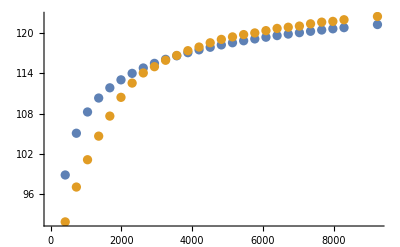

```mathematica
ListPlot[{Cases[cleanData,{ms_,ma2[[1]],tanBeta[[5]],mhEFT_,_}:>{ms,mhEFT}],Cases[cleanData,{ms_,ma2[[1]],tanBeta[[5]],_,mhFS_}:>{ms,mhFS}]}]
```

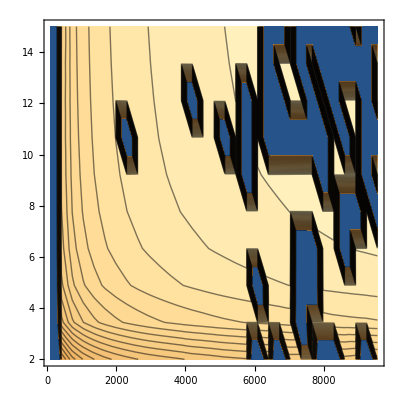

```mathematica
ListContourPlot[Cases[data,{ms_,ma2[[1]],tb_,mhEFT_,_}:>{ms,tb,mhEFT}],Contours->Table[3k,{k,20,50}]]
```

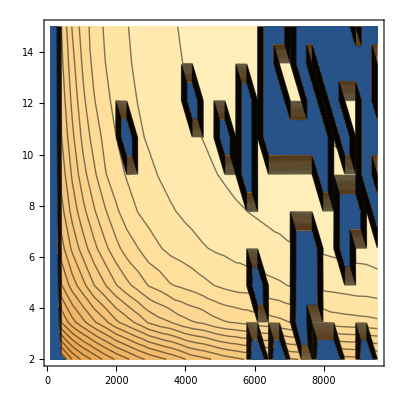

```mathematica
ListContourPlot[Cases[data,{ms_,ma2[[1]],tb_,mhEFT_,mhFS_}:>{ms,tb,mhFS}],Contours->Table[3k,{k,20,50}]]
```